```mathematica
Sum[-1/2^i*(n-2)/pop,{i,0,Infinity}]
```

-(2 (-2+n))/pop

```mathematica
DSolve[n'[t]==r-2 (-2+n[t])/pop,n[t],t]
```

{{n[t]→1/2 (4+pop r)+ⅇ^(-(2 t)/pop) C[1]}}

```mathematica
Solve[1/2 (4+pop r)+ⅇ^(-(2 t)/pop) const==2,const]
```

{{const→-1/2 ⅇ^((2 t)/pop) pop r}}

```mathematica
Simplify[DSolve[-(1/2 (4+pop r)-1/2 pop r ⅇ^(-(2 t)/pop)-1)/pop*f[t]==f'[t],f[t],t]]
```

{{f[t]→ⅇ^(-1/4 ⅇ^(-(2 t)/pop) pop r-t/pop-(r t)/2) C[1]}}

```mathematica
ⅇ^(-1/4 ⅇ^(-2 tau) rho-tau-(rho tau)/2) C[1]/.{tau->0}
```

ⅇ^(-rho/4) C[1]

```mathematica
Simplify[-D[ⅇ^(-1/4 ⅇ^(-2 tau) rho-tau-(rho tau)/2) ⅇ^(rho/4),tau]]
```

1/2 ⅇ^(1/4 (rho-ⅇ^(-2 tau) rho-12 tau-2 rho tau)) (-rho+ⅇ^(2 tau) (2+rho))

```mathematica
Manipulate[Plot[{1/2 ⅇ^(1/4 (rho-ⅇ^(-2 tau) rho-12 tau-2 rho tau)) (-rho+ⅇ^(2 tau) (2+rho)),-Exp[-tau-rho/2*tau^2] (-1-rho tau)},{tau,0,2},PlotRange->{0,5}],{rho,0,50}]
```

### Define the function that convert numbers to the format in file names

```mathematica
number2Printed[number_]:=Module[{returnedString="e",foo,bar,idx,oom},If[number==1,Return["1.0e+00"],If[number==0,Return["0.0e+00"],
If[number<1,
For[idx=1,StringLength[returnedString]==1,idx=idx+1,
foo=Floor[number/10^(-idx)];
If[foo==0,,
bar=Round[(number-foo*10^(-idx))/10^(-idx-1)];
If[StringLength[ToString[idx]]==1,
returnedString=StringJoin[ToString[foo],".",ToString[bar],returnedString,"-0",ToString[idx]],
returnedString=StringJoin[ToString[foo],".",ToString[bar],returnedString,"-",ToString[idx]]
]
]
];
Return[returnedString]
,
oom=(StringLength[ToString[DecimalForm[Floor[number]*1.]]]-2);
foo=Floor[number/10^oom];
bar=Round[(number-foo*10^oom)/10^(oom-1)];
If[StringLength[ToString[oom]]==1,
returnedString=StringJoin[ToString[foo],".",ToString[bar],returnedString,"+0",ToString[oom]],
returnedString=StringJoin[ToString[foo],".",ToString[bar],returnedString,"+",ToString[oom]]
];
Return[returnedString]
];
]
]
]
```

### Import parameters and data

```mathematica
(* combinedParameters= Interpreter[DelimitedSequence["Number",{"[",", ","]"}]][Import[StringJoin[NotebookDirectory[],"combined_parameters.txt"]]];
sequenceLengths= Interpreter[DelimitedSequence["Number",{"[",", ","]"}]][Import[StringJoin[NotebookDirectory[],"sequence_lengths.txt"]]];
populationSizes= Interpreter[DelimitedSequence["Number",{"[",", ","]"}]][Import[StringJoin[NotebookDirectory[],"population_sizes.txt"]]]; *)
combinedParameters= ToExpression[StringReplace[Import[StringJoin[NotebookDirectory[],"combined_parameters.txt"]],{"["->"{","]"->"}"}]];
sequenceLengths= ToExpression[StringReplace[Import[StringJoin[NotebookDirectory[],"sequence_lengths.txt"]],{"["->"{","]"->"}"}]];
populationSizes=  ToExpression[StringReplace[Import[StringJoin[NotebookDirectory[],"population_sizes.txt"]],{"["->"{","]"->"}"}]];
```

```mathematica
histograms=Table[Table[Table[Transpose[
ToExpression[StringReplace[Import[StringJoin[NotebookDirectory[],number2Printed[combinedParameters[[idx1]]],"_",number2Printed[sequenceLengths[[idx2]]],"_",number2Printed[populationSizes[[idx3]]],".txt"]],{"["->"{","]"->"}"}]]
],{idx3,Length[populationSizes]}],{idx2,Length[sequenceLengths]}],{idx1,Length[combinedParameters]}];
```

### Fit scaling factors

```mathematica
predictionFree[tau_,gamma_,beta_,alpha_,combinedParameter_]:=(3gamma*tau^2+beta*combinedParameter*tau+alpha)*Exp[-gamma*tau^3-beta*combinedParameter*tau^2/2-alpha*tau]
```

```mathematica
gammas=Table[0,{idx,Length[combinedParameters]}];
betas=Table[0,{idx,Length[combinedParameters]}];
alphas=Table[0,{idx,Length[combinedParameters]}];
Module[{fit=Table[0,{idx0,Length[combinedParameters]}]},Do[
fit[[idx0]]=NonlinearModelFit[
Flatten[Table[Table[histograms[[idx0,idx1,idx2]],{idx2,Length[populationSizes]}],{idx1,Length[sequenceLengths]}],2],
predictionFree[tau,gamma,beta,alpha,combinedParameters[[idx0]]],{gamma,beta,alpha},tau];
gammas[[idx0]]=fit[[idx0]]["ParameterTable"][[1,1,2,2]];
betas[[idx0]]=fit[[idx0]]["ParameterTable"][[1,1,3,2]];
alphas[[idx0]]=fit[[idx0]]["ParameterTable"][[1,1,4,2]],
{idx0,Length[combinedParameters]}]]
```

General::munfl: Exp[-6525.05] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
newPredictionFree[tau_,a_,b_,rho_]:=-(ⅇ^((-2 a-b+ⅇ^(-a tau) (2 a+b-rho)+rho+a (a+b-rho) tau)/a^2) (a+b-rho+ⅇ^(-a tau) (-2 a-b+rho)))/a
```

```mathematica
zetas=Table[0,{idx,Length[combinedParameters]}];
xis=Table[0,{idx,Length[combinedParameters]}];
Module[{fit=Table[0,{idx0,Length[combinedParameters]}]},Do[
fit[[idx0]]=NonlinearModelFit[
Flatten[Table[Table[histograms[[idx0,idx1,idx2]],{idx2,Length[populationSizes]}],{idx1,Length[sequenceLengths]}],2],
newPredictionFree[tau,zeta,xi,combinedParameters[[idx0]]],{zeta,xi},tau];
zetas[[idx0]]=fit[[idx0]]["ParameterTable"][[1,1,2,2]];
xis[[idx0]]=fit[[idx0]]["ParameterTable"][[1,1,3,2]],
{idx0,Length[combinedParameters]}]]
```

General::munfl: Exp[-1107.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-976.056] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1107.4] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

### Confirm two expressions are same

```mathematica
Simplify[newPredictionFree[tau,2,-4,rho]]
Simplify[1/2 ⅇ^(1/4 (rho-ⅇ^(-2 tau) rho-12 tau-2 rho tau)) (-rho+ⅇ^(2 tau) (2+rho))]
```

1/2 ⅇ^(1/4 (rho-ⅇ^(-2 tau) rho-12 tau-2 rho tau)) (-rho+ⅇ^(2 tau) (2+rho))

1/2 ⅇ^(1/4 (rho-ⅇ^(-2 tau) rho-12 tau-2 rho tau)) (-rho+ⅇ^(2 tau) (2+rho))

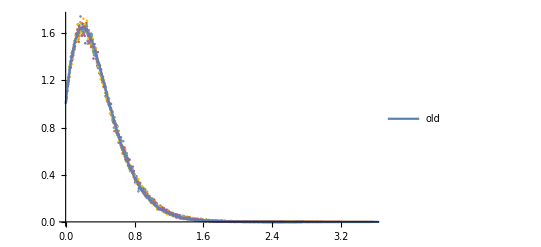

```mathematica
With[{idx0=6},Show[
ListPlot[
Flatten[Table[Table[histograms[[idx0,idx1,idx2]],{idx2,Length[populationSizes]}],{idx1,Length[sequenceLengths]}],1],
ImageSize->Full,PlotRange->All],
Plot[newPredictionFree[tau,2,-4,combinedParameters[[idx0]]],
{tau,0,Transpose[Max[histograms[[idx0,1,1]]]][[1]]*3/2},
PlotRange->Full,PlotStyle->Thick,AxesLabel->{"τ(N×gen)","P(τ)(1/N/gen)"},PlotLegends->Placed[{"old","bad","new fit","new"},Below]]]]
```

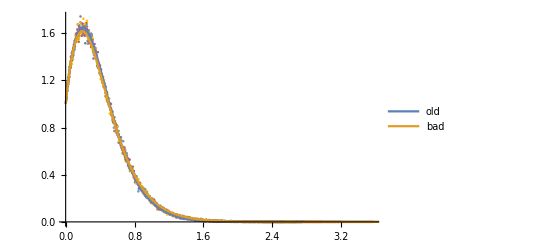

```mathematica
With[{idx0=6},Show[
ListPlot[
Flatten[Table[Table[histograms[[idx0,idx1,idx2]],{idx2,Length[populationSizes]}],{idx1,Length[sequenceLengths]}],1],
ImageSize->Full,PlotRange->All],
Plot[{newPredictionFree[tau,2,-4,combinedParameters[[idx0]]],newPredictionFree[tau,2.5,-5,combinedParameters[[idx0]]]},
{tau,0,Transpose[Max[histograms[[idx0,1,1]]]][[1]]*3/2},
PlotRange->Full,PlotStyle->Thick,AxesLabel->{"τ(N×gen)","P(τ)(1/N/gen)"},PlotLegends->Placed[{"old","bad","new fit","new"},Below]]]]
```

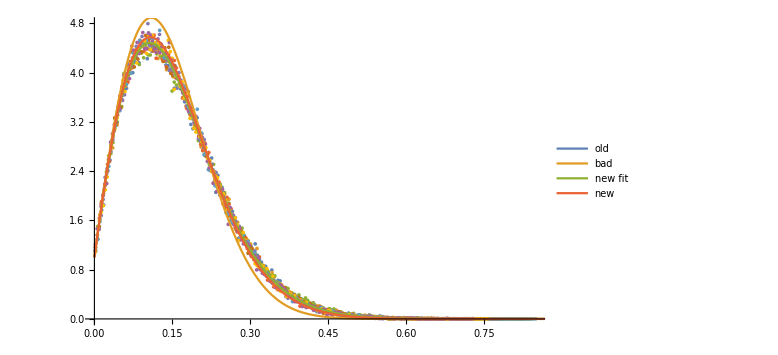
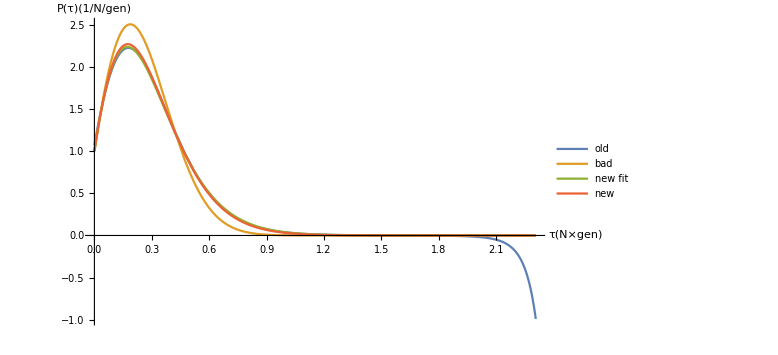

```mathematica
{With[{idx0=12},Show[
ListPlot[
Flatten[Table[Table[histograms[[idx0,idx1,idx2]],{idx2,Length[populationSizes]}],{idx1,Length[sequenceLengths]}],1],
ImageSize->Large,PlotRange->All],
Plot[{predictionFree[tau,gammas[[idx0]],betas[[idx0]],alphas[[idx0]],combinedParameters[[idx0]]],
predictionFree[tau,0,1,1,combinedParameters[[idx0]]],newPredictionFree[tau,zetas[[idx0]],xis[[idx0]],combinedParameters[[idx0]]],
newPredictionFree[tau,2,-4,combinedParameters[[idx0]]]},
{tau,0,Transpose[Max[histograms[[idx0,1,1]]]][[1]]*3/2},
PlotRange->Full,PlotStyle->Thick,AxesLabel->{"τ(N×gen)","P(τ)(1/N/gen)"},PlotLegends->Placed[{"old","bad","new fit","new"},Below]]]],
With[{idx0=7},
Plot[{predictionFree[tau,gammas[[idx0]],betas[[idx0]],alphas[[idx0]],combinedParameters[[idx0]]],
predictionFree[tau,0,1,1,combinedParameters[[idx0]]],
newPredictionFree[tau,zetas[[idx0]],xis[[idx0]],combinedParameters[[idx0]]],
newPredictionFree[tau,2,-4,combinedParameters[[idx0]]]},
{tau,0,Transpose[Max[histograms[[idx0,1,1]]]][[1]]},
PlotRange->Full,PlotStyle->Thick,AxesLabel->{"τ(N×gen)","P(τ)(1/N/gen)"},PlotLegends->Placed[{"old","bad","new fit","new"},Below],ImageSize->Large]]}
```